# 2 DOF

## Data

```mathematica
cellVal={ν->0.3,Yp->2.5*^9,ϵp->3.4*8.85*10^(-12),ϵf->2.7*8.85*10^(-12),EBDp->303*^6,EBDf->157.40*^6,l0->50*^-3/2,w0->10*^-2,tp0->25*^-6,tf0->10*^-6,xi0->3*^-3}

tankVal={d->5,Pt->50*^3,Vtank->1,Vftot->1,f->0.1};

gasVal={patm->101325,Tstd->15+273.15,gammaair->1.4,rhostdair->1.225,(*at T=15°,p=patm*)cv->717.2,(*at T=15°,p=patm*)cp->1.0042       (*at T=15°,p=patm*)};
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,l0→1/40,w0→1/10,tp0→1/40000,tf0→1/100000,xi0→3/1000}

```mathematica
opts={LabelStyle->{Black,Bold}}
```

{LabelStyle→{GrayLevel[0],Bold}}

```mathematica
xmin=tf0/.cellVal;
```

## Model

```mathematica
dtf=dttf/.(Solve[(x/2-tf0/2)/(l0-lc)==(dttf/2)/(l0-lc-(xi-xi0)),dttf]//Flatten)
```

-((tf0-x) (l0-lc-xi+xi0))/(l0-lc)

```mathematica
tf=tf0+dtf;
```

```mathematica
pstrain[]:=Module[{ϵ1,ϵ3,sigma1,wtmp,tptmp,latmp,A1tmp,A2tmp,dAtmp,Cp1tmp,Cf1tmp,C1tmp,dCp2tmp,dCf2tmp,dC2tmp,C2tmp,Volptmp,Volftmp,Voltmp,Vol0tmp,pureUeltmp},
ϵ1=(x-tf0)^2/(8*l0*(l0-lc));
ϵ3=ϵ1*ν/(ν-1);
sigma1=-Yp*ϵ1/(ν^2-1);
wtmp=w0;
tptmp=tp0*(1+ϵ3);
latmp=(l0-lc)+(x-tf0)^2/(8*(l0-lc));
A1tmp=lc*wtmp;
A2tmp=latmp*wtmp;
dAtmp=wtmp*(1+ϵ1);
Cp1tmp=A1tmp*ϵp/tptmp;
Cf1tmp=A1tmp*ϵf/(tf/.x->tf0);
C1tmp=((2/Cp1tmp)+(1/Cf1tmp))^-1;
dCp2tmp=dAtmp*ϵp/tptmp;
dCf2tmp=dAtmp*ϵf/tf;
dC2tmp=((2/dCp2tmp)+(1/dCf2tmp))^-1;
C2tmp=Integrate[dC2tmp,xi];
C2tmp=(C2tmp/. xi->xi0+l0)-C2tmp/. xi->xi0;
Volptmp=2*wtmp*tp0*(lc+latmp);
Volftmp=wtmp*(tf0*lc+((x+tf0)*(l0-lc)/2)+xi0*x);
Voltmp=Volptmp+Volftmp;
Vol0tmp=2*w0*tp0*l0;
pureUeltmp=2*(1/2*(sigma1*ϵ1)*wtmp*tptmp*(lc+latmp));
{w->wtmp,tp->tptmp,la->latmp,A1->A1tmp,A2->A2tmp,dA->dAtmp,Cp1->Cp1tmp,Cf1->Cf1tmp,C1->C1tmp,dCp2->dCp2tmp,dCf2->dCf2tmp,dC2->dC2tmp,C2->C2tmp,Volp->Volptmp,Volf->Volftmp,Vol->Voltmp,Vol0->Vol0tmp,pureUel->pureUeltmp}];
```

```mathematica
res=pstrain[]
```

{w→w0,tp→tp0 (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))),la→l0-lc+(-tf0+x)^2/(8 (l0-lc)),A1→lc w0,A2→w0 (l0-lc+(-tf0+x)^2/(8 (l0-lc))),dA→w0 (1+(-tf0+x)^2/(8 l0 (l0-lc))),Cp1→(lc w0 ϵp)/(tp0 (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν)))),Cf1→(lc w0 ϵf)/tf0,C1→1/(tf0/(lc w0 ϵf)+(2 tp0 (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))))/(lc w0 ϵp)),dCp2→(w0 (1+(-tf0+x)^2/(8 l0 (l0-lc))) ϵp)/(tp0 (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν)))),dCf2→(w0 (1+(-tf0+x)^2/(8 l0 (l0-lc))) ϵf)/(tf0-((tf0-x) (l0-lc-xi+xi0))/(l0-lc)),dC2→1/((tf0-((tf0-x) (l0-lc-xi+xi0))/(l0-lc))/(w0 (1+(-tf0+x)^2/(8 l0 (l0-lc))) ϵf)+(2 tp0 (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))))/(w0 (1+(-tf0+x)^2/(8 l0 (l0-lc))) ϵp)),C2→-1/(8 l0 (tf0-x))w0 (8 l0^2-8 l0 lc+(tf0-x)^2) ϵf Log[8 l0^2 (2 tp0 ϵf+x ϵp) (-1+ν)-8 l0 lc (2 tp0 ϵf+x ϵp) (-1+ν)+2 tp0 (tf0-x)^2 ϵf ν]+1/(8 l0 (tf0-x))w0 (8 l0^2-8 l0 lc+(tf0-x)^2) ϵf Log[8 l0^2 (2 tp0 ϵf+x ϵp) (-1+ν)-8 l0 (-l0 (tf0-x) ϵp+lc (2 tp0 ϵf+x ϵp)) (-1+ν)+2 tp0 (tf0-x)^2 ϵf ν],Volp→2 tp0 w0 (l0+(-tf0+x)^2/(8 (l0-lc))),Volf→w0 (lc tf0+1/2 (l0-lc) (tf0+x)+x xi0),Vol→2 tp0 w0 (l0+(-tf0+x)^2/(8 (l0-lc)))+w0 (lc tf0+1/2 (l0-lc) (tf0+x)+x xi0),Vol0→2 l0 tp0 w0,pureUel→-(tp0 w0 (-tf0+x)^4 (l0+(-tf0+x)^2/(8 (l0-lc))) Yp (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))))/(64 l0^2 (l0-lc)^2 (-1+ν^2))}

```mathematica
eqlcgen=D[pureUel/.res,lc]-V^2/2 D[(C1+C2)/.res,lc]==0
```

-(tp0 w0 (-tf0+x)^6 (l0+(-tf0+x)^2/(8 (l0-lc))) Yp ν)/(512 l0^3 (l0-lc)^4 (-1+ν) (-1+ν^2))-(tp0 w0 (-tf0+x)^6 Yp (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))))/(512 l0^2 (l0-lc)^4 (-1+ν^2))-(tp0 w0 (-tf0+x)^4 (l0+(-tf0+x)^2/(8 (l0-lc))) Yp (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))))/(32 l0^2 (l0-lc)^3 (-1+ν^2))-1/2 V^2 ((w0 (8 l0^2-8 l0 lc+(tf0-x)^2) ϵf (2 tp0 ϵf+x ϵp) (-1+ν))/((tf0-x) (8 l0^2 (2 tp0 ϵf+x ϵp) (-1+ν)-8 l0 lc (2 tp0 ϵf+x ϵp) (-1+ν)+2 tp0 (tf0-x)^2 ϵf ν))-(w0 (8 l0^2-8 l0 lc+(tf0-x)^2) ϵf (2 tp0 ϵf+x ϵp) (-1+ν))/((tf0-x) (8 l0^2 (2 tp0 ϵf+x ϵp) (-1+ν)-8 l0 (-l0 (tf0-x) ϵp+lc (2 tp0 ϵf+x ϵp)) (-1+ν)+2 tp0 (tf0-x)^2 ϵf ν))-(-tf0/(lc^2 w0 ϵf)+(tp0 (-tf0+x)^2 ν)/(4 l0 (l0-lc)^2 lc w0 ϵp (-1+ν))-(2 tp0 (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))))/(lc^2 w0 ϵp))/((tf0/(lc w0 ϵf)+(2 tp0 (1+((-tf0+x)^2 ν)/(8 l0 (l0-lc) (-1+ν))))/(lc w0 ϵp))^2)+(w0 ϵf Log[8 l0^2 (2 tp0 ϵf+x ϵp) (-1+ν)-8 l0 lc (2 tp0 ϵf+x ϵp) (-1+ν)+2 tp0 (tf0-x)^2 ϵf ν])/(tf0-x)-(w0 ϵf Log[8 l0^2 (2 tp0 ϵf+x ϵp) (-1+ν)-8 l0 (-l0 (tf0-x) ϵp+lc (2 tp0 ϵf+x ϵp)) (-1+ν)+2 tp0 (tf0-x)^2 ϵf ν])/(tf0-x))==0

```mathematica
eqlc=eqlcgen/.cellVal//Simplify
```

(21462.9 (0.00001-1. x)^6 (-0.025+lc-0.0000428571 x+2.14286 x^2))/(-0.025+1. lc)^5==(9198.39 (0.00001-1. x)^6 (-0.025+1. lc+0.0001 x-5. x^2))/(-0.025+1. lc)^5+(8585.16 (0.00001-1. x)^4 (-0.025+1. lc+0.0001 x-5. x^2) (-0.025+lc-0.0000428571 x+2.14286 x^2))/(-0.025+1. lc)^5+1/2 V^2 ((1.4042×10^-7 (0.0000397059+1. x) (0.005-0.2 lc-0.00002 x+1. x^2))/((-0.00001+1. x) (-0.0116667+0.466667 lc-293.827 x+11753.1 lc x+1. x^2))-(1.4042×10^-7 (0.0000397059+1. x) (0.005-0.2 lc-0.00002 x+1. x^2))/((-0.00001+1. x) (-0.0146049+0.466667 lc-0.00002 x+11753.1 lc x+1. x^2))+(3.00455×10^-11+4.80728×10^-8 lc^2+4.11443×10^-14 x-2.05721×10^-9 x^2+lc (-2.40364×10^-9-3.29154×10^-12 x+1.64577×10^-7 x^2))/((0.025-1. lc+0.000034235 x-1.71175 x^2)^2)-(2.3895×10^-12 Log[-4.18162×10^-18+lc (1.67265×10^-16+4.2126×10^-12 x)-1.05315×10^-13 x+3.58425×10^-16 x^2])/(-0.00001+1. x)+(2.3895×10^-12 Log[-5.23477×10^-18+lc (1.67265×10^-16+4.2126×10^-12 x)-7.1685×10^-21 x+3.58425×10^-16 x^2])/(-0.00001+1. x))

```mathematica
sollc=Solve[eqlc,lc]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[(21462.9 (0.00001-1. x)^6 (-0.025+lc-0.0000428571 x+2.14286 x^2))/(-0.025+1. lc)^5==(9198.39 (0.00001-1. x)^6 (-0.025+1. lc+0.0001 x-5. x^2))/(-0.025+1. lc)^5+(8585.16 (0.00001-1. x)^4 (-0.025+1. lc+0.0001 x-5. x^2) (-0.025+lc-0.0000428571 x+2.14286 x^2))/(-0.025+1. lc)^5+1/2 V^2 ((1.4042×10^-7 (0.0000397059+1. x) (0.005-0.2 lc-0.00002 x+1. x^2))/((-0.00001+1. x) (-0.0116667+0.466667 lc-293.827 x+11753.1 lc x+1. x^2))-(1.4042×10^-7 (0.0000397059+1. x) (0.005-0.2 lc-0.00002 x+1. x^2))/((-0.00001+1. x) (-0.0146049+0.466667 lc-0.00002 x+11753.1 lc x+1. x^2))+(3.00455×10^-11+4.80728×10^-8 lc^2+4.11443×10^-14 x-2.05721×10^-9 x^2+lc (-2.40364×10^-9-3.29154×10^-12 x+1.64577×10^-7 x^2))/((0.025-1. lc+0.000034235 x-1.71175 x^2)^2)-(2.3895×10^-12 Log[-4.18162×10^-18+lc (1.67265×10^-16+4.2126×10^-12 x)-1.05315×10^-13 x+3.58425×10^-16 x^2])/(-0.00001+1. x)+(2.3895×10^-12 Log[-5.23477×10^-18+lc (1.67265×10^-16+4.2126×10^-12 x)-7.1685×10^-21 x+3.58425×10^-16 x^2])/(-0.00001+1. x)),lc]

```mathematica
lcx=lc/.sollc/.V->1000;
```

```mathematica
Plot3D[lc/.sollc,{x,tf0/.cellVal,6*^-3},{V,1000,6000},AxesLabel->{"x [m]", "V [m]","l_c [m]"},LabelStyle->{GrayLevel[0],Bold},ImageSize->Large]
```

-Graphics3D-

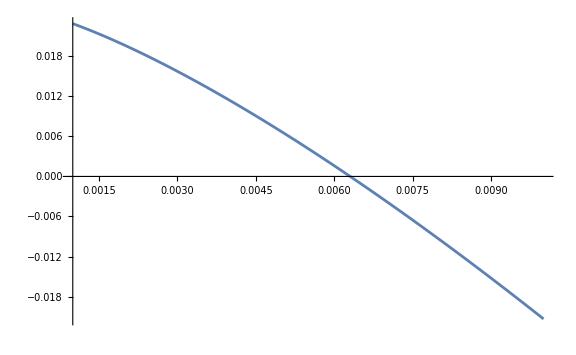

```mathematica
Plot[lc/.sollc/.V->6000,{x,100*xmin,10*^-3},ImageSize->Large]
```

```mathematica
Table[lc/.sollc/.V->0.0001,{x,xmin,10*^-3,10*^-5}] //N
```

{0.025,-15.261,-38.4932,-66.1136,-97.0349,-130.668,-166.634,-204.662,-244.551,-286.14,-329.301,-373.928,-419.929,-467.227,-515.754,-565.452,-616.267,-668.152,-721.066,-774.968,-829.825,-885.605,-942.277,-999.814,-1058.19,-1117.39,-1177.38,-1238.14,-1299.66,-1361.91,-1424.89,-1488.57,-1552.93,-1617.97,-1683.68,-1750.03,-1817.01,-1884.62,-1952.84,-2021.66,-2091.07,-2161.06,-2231.62,-2302.75,-2374.43,-2446.65,-2519.41,-2592.7,-2666.52,-2740.84,-2815.68,-2891.01,-2966.84,-3043.15,-3119.95,-3197.23,-3274.97,-3353.18,-3431.84,-3510.96,-3590.53,-3670.54,-3750.99,-3831.87,-3913.18,-3994.92,-4077.08,-4159.65,-4242.64,-4326.03,-4409.83,-4494.02,-4578.61,-4663.6,-4748.97,-4834.73,-4920.88,-5007.4,-5094.29,-5181.56,-5269.2,-5357.2,-5445.56,-5534.29,-5623.37,-5712.81,-5802.6,-5892.74,-5983.22,-6074.05,-6165.21,-6256.72,-6348.56,-6440.73,-6533.24,-6626.07,-6719.24,-6812.72,-6906.53,-7000.65}

```mathematica
xmin//N
```

0.00001

```mathematica
sollc
```

{lc→Root[107615426158118279704440390393565781685416631557575436050656149556041701000000000-470776921857163444600214052639609150871286279993394726070800000000000000000000000000 V^2-43046170537477371404577111958730166728199150264884666234436010644035018178850213000000 x-644681841614985370821668574704950966853311585407859882275510000000000000000000000 V^2 x+6456925602890621282937518107926399825193420182792245269169070108057003926538606210460635000 x^2+32234092080749268541083428735247548342665579270392994113775500000000000000000000000000 V^2 x^2-430461710570876738347175046557931436838752498341566999263225564762968011882160930027680254647451 x^3+10761543135422010459646452164442322633730035804896293100150305328029806020909736952804184415078450000 x^4-22268992726358200638476237686558101519799572691507659302290872338608399534454485332938242500000000 x^5+371148812631013087943880937329897568152081275696119447405721850302483005423022356832109375000000000000 x^6+45691781027705747076636036035913252437106509809099788545422093234650561402595999800000000000000000000 x^7-571147085320707836901087528050069477906557798441457799358520422326337635526429395000000000000000000000000 x^8-5917520314498830901804204709714000443103454938336689773919163656402444608750000000000000000000000000000 x^9+59175195534001749237587538953577903962586813704435960196638495414136642187500000000000000000000000000000000 x^10+207572360721285122949369875467321301882152661932978722031360576470000000000000000000000000000000000000000 x^11-1729769672677376024578082295561010849017938849441489350261338137250000000000000000000000000000000000000000000 x^12+(-17218468170452913033196106889692072955556185545631471813897994384275719136000000000+131817538120005770106051108503126739684986582129760610397777700000000000000000000000000 V^2+6887387277088773269850293033319729594350668313277895074380036205344073353200773336000000 x+180510915652195903830067200917386270718927243914200767037142800000000000000000000000 V^2 x-1033108094235598224681949363718976786336092586709711140883433510238703087289145799865415288000 x^2-9025545782609795191503360045869313535946362195710038351857140000000000000000000000000000 V^2 x^2+68873873394420205274957801858936178106092203646204070338327577639646460122885045686010491200000000 x^3-1721846879398528965689825141968833441421156659849779769192902953526497395990541425521632980000000000000 x^4+2672280406532932807086925379123430429517990554243175648697879724401103418965681186000000000000000000 x^5-44537921484215016395188842215068054646942791192525509297286535018063942319528348300000000000000000000000 x^6-3655342766257442365679785463868067875334020166723025824098114908658728277600000000000000000000000000000 x^7+45691777477193195513206260363734491405288492634099227538460525877985246700000000000000000000000000000000000 x^8+236700827801926368597820545234546225314997953175425530349341628559000000000000000000000000000000000000000 x^9-2367008278019263685978205452345462253149979531754255303493416285590000000000000000000000000000000000000000000 x^10) #1+(1033108089336413987437331379778499331261747380272984606486659811800110626244000000000-15818104579558147591478698189250982137111105069604474076801454400000000000000000000000000 V^2-413243236090869953791236554342557289481993663637259904303906884279642564291755214876000000 x-20629818931679531866293394390558430939305970733051516232816320000000000000000000000000 V^2 x+61986485520521797058233633582294935466122218902422339323822289542505703326388742760600000000000 x^2+1031490946583976593314669719527921546965298536652575811640816000000000000000000000000000000 V^2 x^2-4132432385850002827382120564388639358547944392543990945417760528308219880697865223280000000000000000 x^3+103310811427771535785198499406270514407300198311148247073362023946881274982323350938000000000000000000000 x^4-106891267436117647446552091550170728340968705332869947227357564126414421193200000000000000000000000000 x^5+1781519418108537318172436502799064891609128166097404669039877522817058517540000000000000000000000000000000 x^6+73106861005968718500987304882031729296690732619346403509112422078672000000000000000000000000000000000000 x^7-913835762574608981262341311025396616208634157741830043863905275983400000000000000000000000000000000000000000 x^8) #1^2+(-27549549025217416039981899380378436822687817349259132629641401016478532717360000000000+1054540305991537151654992511687879172934224309991844352212218080000000000000000000000000000 V^2+11019819614837691687589220576772571572428370394878381341477280101988878574720000000000000000 x+1237789135900771911977603663433505856358358243983090973968979200000000000000000000000000 V^2 x-1652972943650871334617321333902244788870228595784175688107807923917571432540800000000000000000000 x^2-61889456795038595598880183171675292817917912199154548698448960000000000000000000000000000000 V^2 x^2+110198196480927685887644463491209494759010745811014793688223179697711369891520000000000000000000000000 x^3-2754954935776818505173415710386221585741485921149011290309177969430111686168000000000000000000000000000000 x^4+1425217581478938247386359053005973036552418486886215908619239646332800000000000000000000000000000000000 x^5-23753626357982304123105984216766217275873641448103598476987327438880000000000000000000000000000000000000000 x^6) #1^3+(275495490014637899780729209102298382719201155226534872532117729021520000000000000000000-42181612280921123900705870609538200354413782923708924978343398400000000000000000000000000000 V^2-110198196005855159912291683640919353087680462090613949012847091608608000000000000000000000000 x-41259637863359063732586788781116861878611941466103032465632640000000000000000000000000000 V^2 x+16529729400878273986843752546137902963152069313592092351927063741291200000000000000000000000000000 x^2+2062981893167953186629339439055843093930597073305151623281632000000000000000000000000000000000 V^2 x^2-1101981960058551599122916836409193530876804620906139490128470916086080000000000000000000000000000000000 x^3+27549549001463789978072920910229838271920115522653487253211772902152000000000000000000000000000000000000000 x^4) #1^4+(1012358696062415369939080934337721264242337082185217204984829696000000000000000000000000000000 V^2+726169626395119521693527482547656769063570169803413371395134464000000000000000000000000000 V^2 x-36308481319755976084676374127382838453178508490170668569756723200000000000000000000000000000000 V^2 x^2) #1^5+(-13498115969504011394069505737957031643014322848543727928499916800000000000000000000000000000000 V^2-5281233646509960157771108963982958320462328507661188155600977920000000000000000000000000000 V^2 x+264061682325498007888555448199147916023116425383059407780048896000000000000000000000000000000000 V^2 x^2) #1^6+77132091405201023044978048202368391272925118821767723309579714560000000000000000000000000000000 V^2 #1^7&,1]}